# MPO Input File Creator

2 Leg Ladder

### Some Operators

```mathematica
sp=1/2*(PauliMatrix[1]+I*PauliMatrix[2]);
sm=1/2*(PauliMatrix[1]-I*PauliMatrix[2]);
sz=PauliMatrix[3];
sx=PauliMatrix[1];
sy=PauliMatrix[2];
id=IdentityMatrix[2];
```

```mathematica
jw=+KroneckerProduct[sz,sz];
```

```mathematica
ann1L=-KroneckerProduct[sm,sz];
cr1R  =+KroneckerProduct[sp,id];

ann2L=+KroneckerProduct[id,sm];
cr2R  =-KroneckerProduct[sz,sp];
```

```mathematica
ρ1=+KroneckerProduct[sp.sm,id];
ρ2=+KroneckerProduct[id,sp.sm];

ρ1ρ2=+KroneckerProduct[sp.sm,sp.sm];
nTot=ρ1+ρ2;
```

### Symmetry Sectors

```mathematica
sectors={{2,1},{1,1},{1,2},{0,1}};
state[i_]:=
{
(Transpose[ann1L].ann1L)[[i,i]],
(Transpose[ann2L].ann2L)[[i,i]]
}
```

```mathematica
symSecs=Table[{sectors[[i]],"|"<>Table[ToString[state[i][[j]]],{j,1,2}]<>">"},{i,1,Length[sectors]}]//Transpose//TableForm
```

2
1 | 1
1 | 1
2 | 0
1
|11> | |10> | |01> | |00>

```mathematica
giveNonzero[op_]:=Module[{tp,nonzeros},
tp=op;
nonzeros=SparseArray[tp]["NonzeroPositions"];
Table[{{sectors[[nonzeros[[i,2]]]],sectors[[nonzeros[[i,1]]]]},tp[[nonzeros[[i,1]],nonzeros[[i,2]]]]},{i,1,Length[nonzeros]}]
]
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]<>"/MPOS_2Legs"]
```

/Users/andreas/Dropbox/Michele-Matteo-Andreas/simulations/MPOS_2Legs

### Identity

```mathematica
operator =IdentityMatrix[2^2];
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{2,1},{2,1}},1},{{{1,1},{1,1}},1},{{{1,2},{1,2}},1},{{{0,1},{0,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
Export["id.in",string,"String"];
string="";
```

### JW string

```mathematica
operator =jw;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{2,1},{2,1}},1},{{{1,1},{1,1}},-1},{{{1,2},{1,2}},-1},{{{0,1},{0,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
Export["jw.in",string,"String"];
string="";
```

### Hopping Operators

#### Nearest-neighbor transitions

```mathematica
operator =ann1L;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{2,1},{1,2}},-1},{{{1,1},{0,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["ann1L.in",string,"String"];
string="";
```

```mathematica
operator =cr1R;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{1,2},{2,1}},1},{{{0,1},{1,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["cr1R.in",string,"String"];
string="";
```

```mathematica
operator =ann2L;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{2,1},{1,1}},1},{{{1,2},{0,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["ann2L.in",string,"String"];
string="";
```

```mathematica
operator =cr2R;
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["cr2R.in",string,"String"];
string="";
```

### Hopping Operators -- h.c. part of the above

#### Nearest-neighbor transitions

```mathematica
operator =ann1L†;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{1,2},{2,1}},-1},{{{0,1},{1,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["ann1Lct.in",string,"String"];
string="";
```

```mathematica
operator =cr1R†;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{2,1},{1,2}},1},{{{1,1},{0,1}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["cr1Rct.in",string,"String"];
string="";
```

```mathematica
operator =ann2L†;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
```

{{{{1,1},{2,1}},1},{{{0,1},{1,2}},1}}

```mathematica
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["ann2Lct.in",string,"String"];
string="";
```

```mathematica
operator =cr2R†;
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["cr2Rct.in",string,"String"];
string="";
```

### On - Site Transitions

#### Spin Flips

```mathematica
operator =KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp];
opSparse=giveNonzero[operator]
```

{{{{1,2},{1,1}},1},{{{1,1},{1,2}},1}}

```mathematica
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["spin_flips.in",string,"String"];
string="";
```

### Density - density interactions

#### Onsite

```mathematica
operator =1/2*nTot(nTot-IdentityMatrix[2^2]);
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
Export["hubbard.in",string,"String"];
string="";
```

{{{{2,1},{2,1}},1}}

#### Nearest Neighbor

```mathematica
operator =nTot;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
Export["n.in",string,"String"];
string="";
```

{{{{2,1},{2,1}},2},{{{1,1},{1,1}},1},{{{1,2},{1,2}},1}}

```mathematica
operator =ρ1;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
Export["n1.in",string,"String"];
string="";
```

{{{{2,1},{2,1}},1},{{{1,1},{1,1}},1}}

```mathematica
operator =ρ2;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
Export["n2.in",string,"String"];
string="";
```

{{{{2,1},{2,1}},1},{{{1,2},{1,2}},1}}

### Coupling Constants

```mathematica
t=1;
J=1;
Ω=1;
B=1;
μ0=1;
μ=1;
Ωint=1;
kF=1;
```

```mathematica
constants={};
constants=Join[constants,{{1//N}}];
constants=Join[constants,{{+t*Exp[-I*B/2]//N}}];
constants=Join[constants,{{+t*Exp[+I*B/2]//N}}];
constants=Join[constants,{{-t*Exp[-I*B/2]//N}}];
constants=Join[constants,{{-t*Exp[+I*B/2]//N}}];
constants=Join[constants,{{+t*Exp[+I*B/2]//N}}];
constants=Join[constants,{{+t*Exp[-I*B/2]//N}}];
constants=Join[constants,{{-t*Exp[+I*B/2]//N}}];
constants=Join[constants,{{-t*Exp[-I*B/2]//N}}];
constants=Join[constants,{{μ0+μ//N}}];
constants=Join[constants,{{μ0-μ//N}}];
constants=Join[constants,{{J//N}}];
constants=Join[constants,{{Ωint*Exp[+I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[-I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[-I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[+I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[-I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[+I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[+I*4*kF]//N}}];
constants=Join[constants,{{Ωint*Exp[-I*4*kF]//N}}];
```

```mathematica
string="F ! is site-dependent\n20! number of specified terms\n----------------------\n";
For[i=1,i≤ 20,string=string<>""<>ToString[Re[constants[[i,1]]]]<>" "<>ToString[Im[constants[[i++,1]]]]<>"";];
string=string<>"\nEND_INTERACTIONS";
Export["../couplings.in",string,"String"]
```

```mathematica
string
```

### Observables

#### Occupation number

```mathematica
ρ1=KroneckerProduct[sp.sm,id];
```

```mathematica
operator =ρ1;
opSparse=giveNonzero[operator]
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["n2.in",string,"String"];
string="";
```

```mathematica
operator =KroneckerProduct[id,KroneckerProduct[sp.sm,KroneckerProduct[id,id]]];
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["n2.in",string,"String"];
string="";
```

```mathematica
operator =KroneckerProduct[id,KroneckerProduct[id,KroneckerProduct[sp.sm,id]]];
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["n3.in",string,"String"];
string="";
```

```mathematica
operator =KroneckerProduct[id,KroneckerProduct[id,KroneckerProduct[id,sp.sm]]];
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["n4.in",string,"String"];
string="";
```

#### Correlations

```mathematica
operator =jordW;
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
Export["jordWString.in",string,"String"];
string="";
```

#### Double annihilators

```mathematica
operator =ann1L.ann2L;
opSparse=giveNonzero[operator];
numOfNonzeros=opSparse//Length;
string=
ToString[numOfNonzeros]<>"\t\t\t\t\t\t% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)\n";
For[i=1,i≤ Length[opSparse],
string=string<>"%%%%%%%%%%%%%%%\n"<>ToString[opSparse[[i,1,2,1]]]<>" "<>ToString[opSparse[[i,1,2,2]]]<>"\t\t\t\t\t\t% bottom sector / deg. index\n"<>ToString[opSparse[[i,1,1,1]]]<>" "<>ToString[opSparse[[i,1,1,2]]]<>"\t\t\t\t\t\t% top sector / deg. index\n"<>"("<>ToString[Re[opSparse[[i,2]]]]<>"d0,"<>ToString[Im[opSparse[[i,2]]]]<>"d0)\t\t\t% element value\n";
i++;
];
```

```mathematica
string
```

1						% number of non-zero elements of the physical operator (d x d matrix,sectors are the physical ones)
%%%%%%%%%%%%%%%
0 1						% bottom sector / deg. index
2 1						% top sector / deg. index
(1d0,0d0)			% element value

```mathematica
Export["jordWString.in",string,"String"];
string="";
```

Benchmark

```mathematica
L=4;
t=1.;
g=1.;
χ=0.5π;
m=0.;
NP = L;

tt =t*MatrixExp[ⅈ*χ/2 PauliMatrix[3]];
gg = g*PauliMatrix[1];
mm = m*PauliMatrix[1];

Ham=ConstantArray[0,{2L,2L}];

Do[
Ham[[2ii-1;;2ii, 2ii+1 ;; 2ii+2]] = tt+gg;
,{ii,1,L-1}];
(* PBC term *)
(*Ham[[2L-1;;2L, 1 ;; 2]] = tt+gg;*)
Ham = Ham + Ham†;
Do[
Ham[[2ii-1;;2ii, 2ii-1 ;; 2ii]] = mm;
,{ii,1,L}];
{eval,evec}=Eigensystem[Ham];
order=Ordering[eval];
eval=eval[[order]];
evec=evec[[order]];
GSenergy=Total[eval[[;;NP]]]*2
```

-10.8371

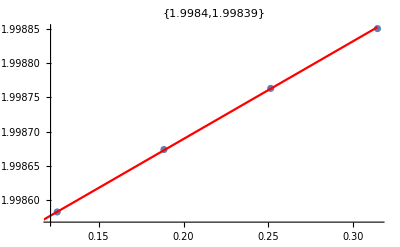

{{0.0628319,-81.4258},{0.125664,-81.4296},{0.188496,-81.4333},{0.251327,-81.437},{0.314159,-81.4405},{0.376991,-81.444}}

```mathematica
L=32;
cphi={};
ephi={};
Do[
t=1.;
g=-t;
χ=π;
m=1.;
NP =Floor[(ρ=1.)*L];
(ρ=NP/L);
If[OddQ[NP],NP=NP-1;(ρ=NP/L)];

tt =t*MatrixExp[ⅈ*χ/2*PauliMatrix[3]];
gg = g*PauliMatrix[1];
mm = m*PauliMatrix[1];

Ham=ConstantArray[0,{2L,2L}];
Do[
Ham[[2ii-1;;2ii, 2ii+1 ;; 2ii+2]] = tt+gg;
,{ii,1,L-1}];
Do[
Ham[[2ii-1;;2ii, 2ii-1 ;; 2ii]] = mm;
,{ii,1,L}];
(* PBC term *)
Ham[[2L-1;;2L,1;;2]]=(tt+gg)*Exp[+ⅈ*phi];
Ham=Ham+Ham†;
{eval,evec}=Chop[Eigensystem[Ham]];
order=Ordering[eval];
eval=eval[[order]];
evec=evec[[order]];
GSenergy=Total[eval[[;;NP]]];
AppendTo[ephi,{phi,GSenergy}];
GSmodes = evec[[;;NP]];
SPGF=Chop[GSmodesᵀ.GSmodes*];
ups=;;;;2;
downs=2;;;;2;
,{phi,δ=.01*2π,Min[6δ,2π],δ}]
ephi[[All,2]]-ephi[[1,2]]//ListPlot;
(ephipr=Table[{Mean[{ephi[[i,1]],ephi[[i+1,1]]}],(ephi[[i+1,2]]-ephi[[i,2]])/δ},{i,1,Length[ephi]-1}])//ListPlot;
(ephiprpr=Table[{Mean[{ephipr[[i,1]],ephipr[[i+1,1]]}],L π(ephipr[[i+1,2]]-ephipr[[i,2]])/δ},{i,1,Length[ephipr]-1}])//ListPlot;
Show[ListPlot[ephiprpr=Table[{ephi[[i+1,1]],L π(ephi[[i+2,2]]+ephi[[i,2]]-2ephi[[i+1,2]])/δ^2},{i,1,Length[ephi]-2}],GridLines->{{},{exact=π/L(Cot[π/(2L)]Cos[π/2(1-ρ)])}},GridLinesStyle->Red],fit=LinearModelFit[ephiprpr,{1,x},x,Weights->1/Range[Length[ephiprpr]]^2];Plot[fit["BestFit"],{x,0,Max[ephiprpr[[All,1]]]},PlotStyle->Red],PlotLabel->{fit["BestFit"][[1]],N[exact]}]
ephi
```